-Graphics-

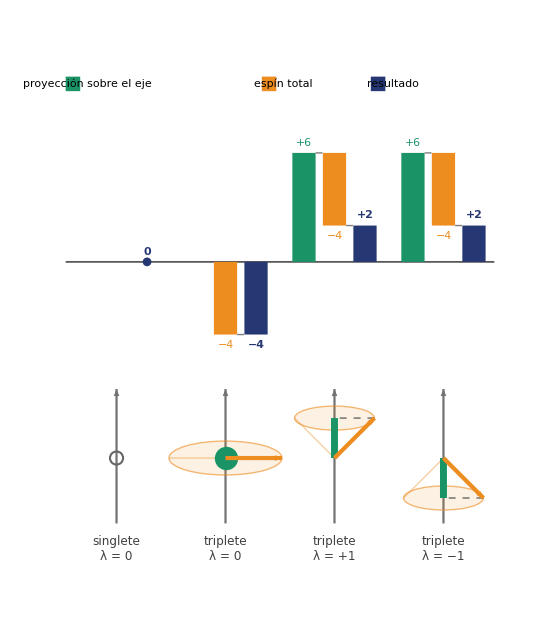

```mathematica
(* ================================================================== *)
(*  OPERADOR TENSOR  S12 = 3(σ1·r)(σ2·r)/r.b2 − σ1·σ2                   *)
(*  Figura 1: helicidad λ = S·r/r (proyección del espín sobre el eje)  *)
(*  Figura 2: S12 = 6λ.b2 − 2S.b2  (descomposición en cascada)             *)
(* ================================================================== *)

ClearAll[mostrarSimbolos, mostrarValores, colLam, colSpin, colTen, colEje, colP, colN,
  fmt, panelHel, figHel, esc, anchoB, sepB, estados, xs, cascada, icono, etiqCol,
  leyenda, figS12];

(* ---------- Opciones de visualización ---------- *)
mostrarSimbolos = True;   (* letras r, S, λ y títulos de los paneles *)
mostrarValores  = True;   (* números sobre las barras de la figura 2 *)

(* ---------- Paleta común ---------- *)
colLam  = RGBColor[0.10, 0.58, 0.40];   (* helicidad λ: proyección sobre el eje *)
colSpin = RGBColor[0.93, 0.55, 0.12];   (* espín total S *)
colTen  = RGBColor[0.15, 0.22, 0.45];   (* resultado: operador tensor *)
colEje  = GrayLevel[0.45];              (* eje r que une los nucleones *)
colP    = RGBColor[0.80, 0.25, 0.20];   (* protón *)
colN    = RGBColor[0.35, 0.50, 0.75];   (* neutrón *)

fmt[v_] := Which[v > 0, "+" <> ToString[v], v < 0, "−" <> ToString[-v], True, "0"];

(* ================================================================== *)
(* FIGURA 1 - Helicidad: un panel por cada valor de λ (triplete, S = 1) *)
(* El espín total tiene módulo √2; solo su proyección sobre el eje    *)
(* está definida, así que el vector "gira" sobre un cono.              *)
(* ================================================================== *)
panelHel[m_] := Module[{rho = Sqrt[2.0 - m^2], tip, z0 = 2.3},
  tip = {rho, 0, m};
  Graphics3D[{
    (* eje r que une protón y neutrón *)
    {colEje, Arrowheads[0.045], Arrow[Tube[{{0, 0, -3.0}, {0, 0, 3.0}}, 0.022]]},
    {colP, Sphere[{0, 0, z0}, 0.30]},
    {colN, Sphere[{0, 0, -z0}, 0.30]},

    (* cono (o disco si λ = 0) de orientaciones posibles del espín *)
    {Opacity[0.12], colSpin, Specularity[0],
     If[m == 0,
      Cylinder[{{0, 0, -0.01}, {0, 0, 0.01}}, rho],
      Cone[{{0, 0, m}, {0, 0, 0}}, rho]]},
    {colSpin, Opacity[0.45], AbsoluteThickness[0.8],
     Table[Line[{{0, 0, 0}, {rho Cos[t], rho Sin[t], m}}], {t, 0, 11 Pi/6, Pi/6}]},
    {colSpin, Opacity[0.9], AbsoluteThickness[1.5],
     Line[Table[{rho Cos[t], rho Sin[t], m}, {t, 0, 2 Pi, Pi/30}]]},

    (* vector espín S *)
    {colSpin, Arrowheads[0.055], Arrow[Tube[{{0, 0, 0}, tip}, 0.045]]},

    (* proyección sobre el eje = helicidad λ *)
    If[m == 0,
     {colLam, Sphere[{0, 0, 0}, 0.11]},
     {{colLam, Tube[{{0, 0, 0}, {0, 0, m}}, 0.085]},
      {GrayLevel[0.35], Dashed, AbsoluteThickness[1.2], Line[{tip, {0, 0, m}}]}}],

    (* símbolos opcionales *)
    If[mostrarSimbolos, {
      Text[Style[OverHat["r"], 16], {0.3, 0, 3.15}],
      Text[Style["S", 16, Bold, colSpin], tip + {0.18, 0, 0.22}],
      Text[Style["λ", 16, Bold, colLam], {-0.28, 0, If[m == 0, 0.3, m/2]}]}, {}]
   },
   Boxed -> False, Lighting -> "Neutral", SphericalRegion -> True,
   PlotRange -> {{-1.7, 1.7}, {-1.7, 1.7}, {-3.3, 3.3}},
   BoxRatios -> {1, 1, 1.9},
   ViewPoint -> {1.9, -2.6, 1.0}, ViewVertical -> {0, 0, 1},
   ImageSize -> 300,
   PlotLabel -> If[mostrarSimbolos, Style["λ = " <> fmt[m], 15], None]]
];

figHel = GraphicsRow[panelHel /@ {1, 0, -1}, Spacings -> 10, ImageSize -> 900];

(* ================================================================== *)
(* FIGURA 2 - Cascada: S12 = (término de proyección) − (término de S.b2) *)
(* Por columna: verde sube, naranja baja (colgando del verde), azul    *)
(* oscuro es el resultado. Debajo, el esquema del estado de espín.     *)
(* ================================================================== *)
esc    = 0.25;    (* escala vertical (solo estética) *)
anchoB = 0.32;    (* ancho de cada barra *)
sepB   = 0.42;    (* separación entre las tres barras de una columna *)

estados = {{0, 0}, {1, 0}, {1, 1}, {1, -1}};   (* {S, λ} *)
xs = {1, 2.5, 4, 5.5};

cascada[x_, S_, m_] := Module[{a = esc 6 m^2, b = esc 2 S (S + 1), net, xa, xb, xc},
  net = a - b;
  xa = x - sepB; xb = x; xc = x + sepB;
  {
   (* aporte de la proyección: sube *)
   If[a > 0, {colLam, Rectangle[{xa - anchoB/2, 0}, {xa + anchoB/2, a}]}, {}],
   (* aporte del espín total: baja, colgando del anterior *)
   If[b > 0, {colSpin, Rectangle[{xb - anchoB/2, a - b}, {xb + anchoB/2, a}]}, {}],
   (* resultado *)
   If[net == 0,
    {colTen, Disk[{xc, 0}, 0.06]},
    {colTen, Rectangle[{xc - anchoB/2, Min[0, net]}, {xc + anchoB/2, Max[0, net]}]}],
   (* conectores *)
   {GrayLevel[0.5], Dashed, AbsoluteThickness[1],
    If[a > 0 && b > 0, Line[{{xa + anchoB/2, a}, {xb - anchoB/2, a}}], {}],
    If[b > 0, Line[{{xb + anchoB/2, net}, {xc - anchoB/2, net}}], {}]},
   (* valores numéricos opcionales *)
   If[mostrarValores, {
     If[a > 0, Text[Style[fmt[Round[6 m^2]], 11, colLam], {xa, a + 0.14}], {}],
     If[b > 0, Text[Style[fmt[-Round[2 S (S + 1)]], 11, colSpin], {xb, net - 0.14}], {}],
     Text[Style[fmt[Round[6 m^2 - 2 S (S + 1)]], 11, Bold, colTen],
      {xc, If[net ≥ 0, net + 0.14, net - 0.14]}]}, {}]
  }];

(* esquema del estado de espín respecto al eje r (vertical) *)
icono[x0_, y0_, S_, m_] := Module[{sc = 0.55, z, rho, ell = 0.3},
  z = m sc;
  rho = If[S == 0, 0., Sqrt[S (S + 1) - m^2]] sc;
  {
   {colEje, AbsoluteThickness[1.6], Arrowheads[0.022],
    Arrow[{{x0, y0 - 0.9}, {x0, y0 + 0.95}}]},
   If[S == 0,
    {GrayLevel[0.4], AbsoluteThickness[1.5], Circle[{x0, y0}, 0.09]},   (* espín nulo *)
    {
     {colSpin, Opacity[0.12], Disk[{x0, y0 + z}, {rho, ell rho}]},
     {colSpin, Opacity[0.6], AbsoluteThickness[1], Circle[{x0, y0 + z}, {rho, ell rho}]},
     {colSpin, Opacity[0.4], AbsoluteThickness[1],
      Line[{{x0 - rho, y0 + z}, {x0, y0}, {x0 + rho, y0 + z}}]},
     If[m ≠ 0,
      {{GrayLevel[0.4], Dashed, AbsoluteThickness[1],
        Line[{{x0 + rho, y0 + z}, {x0, y0 + z}}]},
       {colLam, AbsoluteThickness[5], Line[{{x0, y0}, {x0, y0 + z}}]}},
      {colLam, PointSize[0.03], Point[{x0, y0}]}],
     {colSpin, AbsoluteThickness[3], Arrowheads[0.03], Arrow[{{x0, y0}, {x0 + rho, y0 + z}}]}
    }]
  }];

etiqCol[x_, S_, m_] := Text[
   Style[Column[Flatten[{
       If[S == 0, "singlete", "triplete"],
       If[mostrarSimbolos, {"λ = " <> fmt[m]}, {}]}], Center],
    12, GrayLevel[0.25]], {x, -3.95}];

leyenda = {
   {colLam, Rectangle[{0.3, 2.35}, {0.5, 2.55}]},
   Text[Style["proyección sobre el eje", 11], {0.6, 2.45}, {-1, 0}],
   {colSpin, Rectangle[{3.0, 2.35}, {3.2, 2.55}]},
   Text[Style["espín total", 11], {3.3, 2.45}, {-1, 0}],
   {colTen, Rectangle[{4.5, 2.35}, {4.7, 2.55}]},
   Text[Style["resultado", 11], {4.8, 2.45}, {-1, 0}]};

figS12 = Graphics[{
    {GrayLevel[0.35], AbsoluteThickness[1.3], Line[{{0.3, 0}, {6.2, 0}}]},   (* cero *)
    MapThread[cascada[#1, #2[[1]], #2[[2]]] &, {xs, estados}],
    MapThread[icono[#1, -2.7, #2[[1]], #2[[2]]] &, {xs, estados}],
    MapThread[etiqCol[#1, #2[[1]], #2[[2]]] &, {xs, estados}],
    leyenda},
   PlotRange -> {{0.1, 6.4}, {-4.4, 2.8}},
   ImageSize -> 560];

(* ---------- Mostrar ---------- *)
Print[figHel]; Print[figS12];

(* Exportar (opcional):
   SetDirectory[NotebookDirectory[]];
   Export["helicidad.png", figHel, ImageResolution -> 300];
   Export["S12_cascada.png", figS12, ImageResolution -> 300];
*)
```